```mathematica
t={7,14,21,28,35,42}
P={8,41,133,250,280,297}
```

{7,14,21,28,35,42}

{8,41,133,250,280,297}

```mathematica
N[Log[P]]
```

{2.07944,3.71357,4.89035,5.52146,5.63479,5.69373}

```mathematica
t^2
```

{49,196,441,784,1225,1764}

```mathematica
N[t*Log[P]]
```

{14.5561,51.99,102.697,154.601,197.218,239.137}

```mathematica
Total[t^2]
```

4459

```mathematica
Total[t]
```

147

```mathematica
N[Total[t*Log[P]]]
```

760.199

```mathematica
N[Total[Log[P]]]
```

27.5333

```mathematica
Solve[{4459b+147a==760.2,147b+6a==27.53}]
```

{{a→2.13933,b→0.0999592}}

```mathematica
ⅇ^2.14
```

8.49944

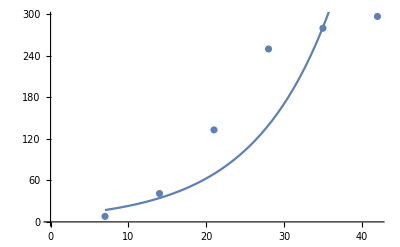

```mathematica
Show[{ListPlot[Transpose[{t,P}]],Plot[8.5*ⅇ^(0.1x),{x,7,42}]}]
```

```mathematica
x={5,10,20,30,40,50,60,70,80}*10^-3
y={0,19,57,94,134,173,216,256,297}*10^-5
```

{1/200,1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25}

{0,19/100000,57/100000,47/50000,67/50000,173/100000,27/12500,8/3125,297/100000}

```mathematica
N[Total[x^2]]
```

0.020425

```mathematica
N[Total[x*y]]
```

0.000728

```mathematica
Solve[Total[x^2]a==Total[x*y]]
```

{{a→728/20425}}

```mathematica
N[{{a->728/20425}}]
```

{{a→0.0356426}}

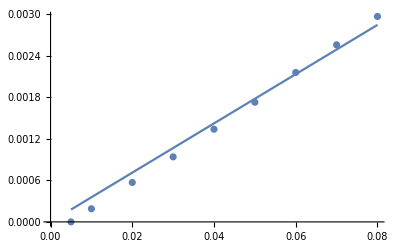

```mathematica
Show[{ListPlot[Transpose[{x,y}]],Plot[0.0356*x,{x,5*10^-3,80*10^-3}]}]
```

```mathematica
N[Total[x]]
```

0.365

```mathematica
N[Total[y]]
```

0.01246

```mathematica
N[Solve[{Total[x^2]*a+Total[x]*b==Total[x*y],Total[x]*a+9b==Total[y]}]]
```

{{a→0.0396067,b→-0.000221828}}

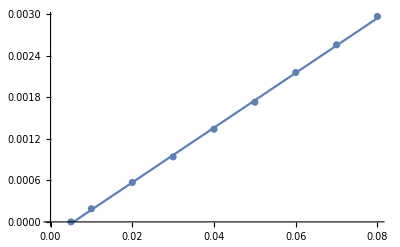

```mathematica
Show[{ListPlot[Transpose[{x,y}]],Plot[0.0396x-0.000222,{x,5*10^-3,80*10^-3}]}]
```

```mathematica
l={14.5,12.5,17.25,14.5,12.625,17.75,14.125,12.625}
w={27,17,41,26,17,49,23,16}
```

{14.5,12.5,17.25,14.5,12.625,17.75,14.125,12.625}

{27,17,41,26,17,49,23,16}

```mathematica
Total[w*l^3]/Total[l^6]
```

0.00843676

```mathematica
g={9.75,8.375,11.0,9.75,8.5,12.5,9.0,8.5}
```

{9.75,8.375,11.,9.75,8.5,12.5,9.,8.5}

```mathematica
Total[w*l*g^2]/Total[l^2*g^4]
```

0.0186751

```mathematica
Total[w*g^3]/Total[g^6]
```

0.0275782

```mathematica
Total[w*l^2*g]/Total[l^4*g^2]
```

0.0125839

```mathematica
Total[(w-0.00844l^3)^2]
```

12.1693

```mathematica
Total[(w-0.0187l*g^2)^2]
```

17.6832

```mathematica
Total[(w-0.0276g^3)^2]
```

54.2605

```mathematica
Total[(w-0.0126g*l^2)^2]
```

3.39977

```mathematica
Max[Abs[w-0.00844l^3]]
```

2.32212

```mathematica
Max[Abs[w-0.0187l*g^2]]
```

2.86328

```mathematica
Max[Abs[w-0.0276g^3]]
```

4.90625

```mathematica
Max[Abs[w-0.0126g*l^2]]
```

1.17079